```mathematica
(*(-h^2d^2/dx^2+x^2/2)*psi=e* psi
p^2/2+x^2/2=e*)
s
s:=1/3;

N[cos[3]]
N[Cos[3]]
N[s]
```

1/3

cos[3.]

-0.989992

0.333333

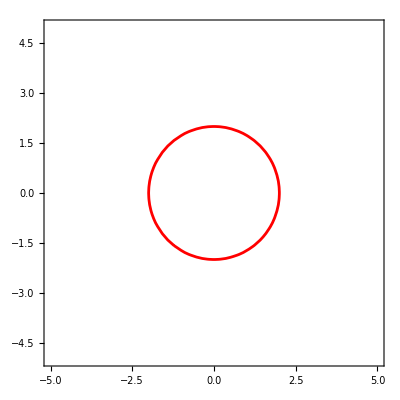

{{x→-2},{x→2}}

```mathematica
(*линия уровня*)
ContourPlot[p^2/2+x^2/2==2,{x,-5,5},{p,-5,5},ContourStyle->Red]
(*решить систему Гамильтона*)
(*задали функцию*)
H[x_,p_]:=p^2/2+x^2/2;
(*частные производныe*)
Hx[x_,p_]:=(D[H[y,p],y])/.y->x;
Hp[x_,p_]:=(D[H[x,q],q])/.q->p;
```

```mathematica
Solve[x^5+a*x+b==0,x]
NSolve[x^5+3*x+2==0,x]
sol
sol[[1]]
x/.sol[[1]]
```

{{x→Root[b+a #1+#1^5&,1]},{x→Root[b+a #1+#1^5&,2]},{x→Root[b+a #1+#1^5&,3]},{x→Root[b+a #1+#1^5&,4]},{x→Root[b+a #1+#1^5&,5]}}

{{x→-0.748468-0.995434 ⅈ},{x→-0.748468+0.995434 ⅈ},{x→-0.632835},{x→1.06489-0.950546 ⅈ},{x→1.06489+0.950546 ⅈ}}

{{x→-2},{x→2}}

{x→-2}

-2

{{P[t]→2 Cos[t],X[t]→2 Sin[t]}}

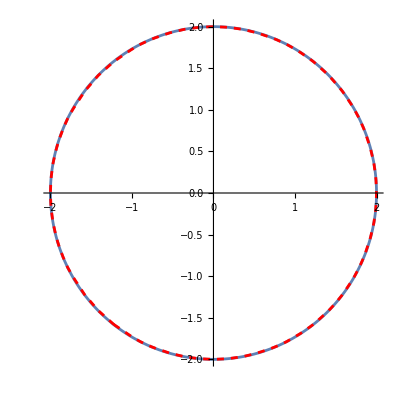

```mathematica
DSolve[X'[t]==Hp[X[t],P[t]]&&P'[t]==-Hx[X[t],P[t]]&&X[0]==0&&P[0]==2,{X[t],P[t]},t]
Show[ParametricPlot[{2 Sin[t],2 Cos[t]},{t,0,2*Pi}],ContourPlot[p^2/2+x^2/2==2,{x,-5,5},{p,-5,5},ContourStyle->{Red,Dashed}]]
```

{{u[x]→C[2] ParabolicCylinderD[-6,ⅈ √2 x]+C[1] ParabolicCylinderD[5,√2 x]}}

-0.121705

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

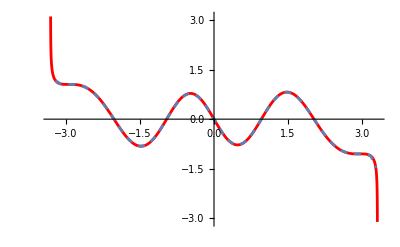

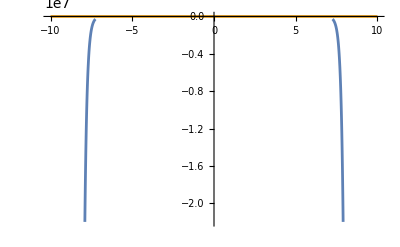

```mathematica
Clear[n]
n:=5;
h:=1;
e:=h*( n+1/2);
(*Plot[e,{n,1,2}]
D[e,n]*)
(*S1[x_]:=Integrate[Sqrt[2*e-y^2],{y,-Sqrt[2*e],x},Assumptions->x>-Sqrt[2*e]&&x<Sqrt[2*e]]*)
S1[x_,n_]:=1/4 (π+2 n π+2 x √(1+2 n-x^2)+(2+4 n) ArcTan[x/(√(1+2 n-x^2))]);
S2[x_,n_]:=-S1[x,n];
J[x_]:=Sqrt[2*e-x^2];
x1:=-Sqrt[2*e];
x2:=Sqrt[2*e];
(*Plot[{Exp[I*S1[x]/h]/Sqrt[Abs[J[x]]]+Exp[-I*Pi/2]*Exp[I*S1[x]/h]/Sqrt[Abs[J[x]]],Exp[I*S1[x]/h]/Sqrt[Abs[J[x]]]+Exp[I*Pi/2]*Exp[I*S1[x]/h]/Sqrt[Abs[J[x]]]},{x,x1,x2}]*)
DSolve[-h^2/2*u''[x]+x^2/2*u[x]==e*u[x],u[x],x]
con:=(((Re[Exp[I*S1[x,n]/h]/Sqrt[Abs[J[x]]]+Exp[-I*Pi/2]*Exp[I*S1[x,n]/h]/Sqrt[Abs[J[x]]]]))/.x->-0.5)/((ParabolicCylinderD[5,√2 x])/.x->-0.5);
N[con]
Show[Plot[con*ParabolicCylinderD[5,√2 x],{x,x1,x2},PlotStyle->Red],ListPlot[Table[{x,Re[Exp[I*S1[x,n]/h]/Sqrt[Abs[J[x]]]+Exp[-I*Pi/2]*Exp[I*S1[x,n]/h]/Sqrt[Abs[J[x]]]]},{x,x1,x2,0.1}],Joined->True,PlotStyle->{Dashed}]]
Plot[{ParabolicCylinderD[-6,ⅈ √2 x],ParabolicCylinderD[5,√2 x]},{x,-10,10}]
(*S2[x_]:=Integrate[-Sqrt[2*e-y^2],{y,-Sqrt[2*e],x},Assumptions->x>-Sqrt[2*e]&&x<Sqrt[2*e]]*)
```

11/2

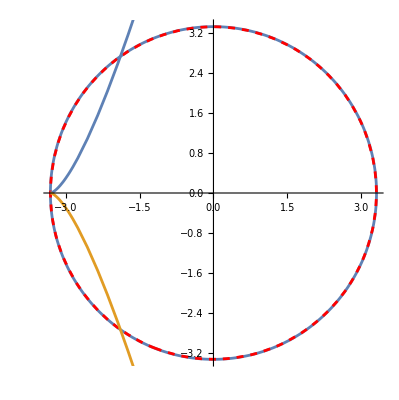

5/2

```mathematica
n:=5;
e
Show[ParametricPlot[{Sqrt[2*e]*Sin[t],Sqrt[2*e]*Cos[t]},{t,0,2*Pi}],ContourPlot[p^2/2+x^2/2==e,{x,-5,5},{p,-5,5},ContourStyle->{Red,Dashed}],Plot[{S1[x,n],S2[x,n]},{x,-5,5}]]
```

```mathematica
Integrate[Sqrt[2*e-y^2],{y,-Sqrt[2*e],x},Assumptions->x>-Sqrt[2*e]&&x<Sqrt[2*e]]
```

1/4 (π+2 n π+2 x √(1+2 n-x^2)+(2+4 n) ArcTan[x/(√(1+2 n-x^2))])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3.31185905043207924614012682695829425938427448272705078125}. NIntegrate obtained 17.2788+0.0414874 ⅈ and 0.0000585664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3.314037739081064970481094178467174060642719268798828125}. NIntegrate obtained 17.2788+0.135939 ⅈ and 0.0000477318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3.31220181039960104296682175117894075810909271240234375}. NIntegrate obtained 17.2788+0.414579 ⅈ and 0.0000403657 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

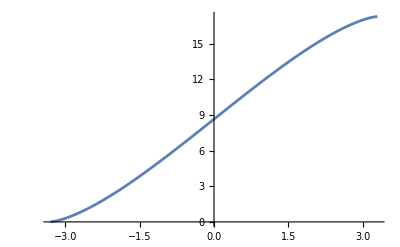

```mathematica
S11[x_]:=NIntegrate[Sqrt[2*e-y^2],{y,-Sqrt[2*e],x}]
ListPlot[Table[{x,S11[x]},{x,-5,5,0.1}],Joined->True]
```

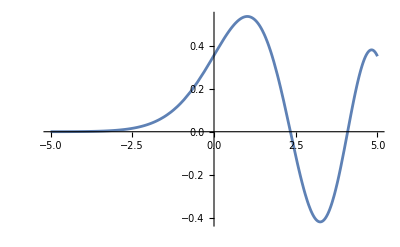

```mathematica
Plot[AiryAi[-x],{x,-5,5}]
```